### Start choosing the example:

```mathematica
t=27;
beta = 0;
A = 0;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{1,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{2,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,U1->0}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[2+j1214-j1218+jt1221]&&NonNegative[j1214]&&NonNegative[jt1221]&&NonNegative[j1218]&&NonNegative[jt1221]&&NonNegative[j1214]&&NonNegative[2-j1218+jt1221]&&NonNegative[j1218-jt1221]&&NonNegative[j1214]&&NonNegative[2-j1218+jt1221]&&NonNegative[jt1221]&&NonNegative[j1218-jt1221]&&NonNegative[-j1214+j1218-u1233+u1234]&&NonNegative[j1214-j1218+u1233-u1234]&&NonNegative[u1233-u1236]&&NonNegative[-j1214+j1218+u1234-u1236]&&NonNegative[2+j1214-j1218-u1233+u1234]&&NonNegative[2+j1214-j1218-u1233]&&NonNegative[-2-j1214+j1218+u1233-u1234]&&NonNegative[-u1234]&&(jt1221==0||2+j1214-j1218+jt1221==0)&&(j1218==0||j1214==0)&&(jt1221==0||j1214==0)&&(j1214==0||jt1221==0)&&(jt1221==0||-j1214+j1218-u1233+u1234==0)&&(j1214==0||j1214-j1218+u1233-u1234==0)&&(2-j1218+jt1221==0||u1233-u1236==0)&&(j1218-jt1221==0||-j1214+j1218+u1234-u1236==0)&&(j1214==0||2+j1214-j1218-u1233+u1234==0)&&(2-j1218+jt1221==0||2+j1214-j1218-u1233==0)&&(jt1221==0||-2-j1214+j1218+u1233-u1234==0)&&(j1218-jt1221==0||-u1234==0)
and the rules are:
<|j1213→2+j1214-j1218+jt1221,j1215→2,j1216→2,j1217→jt1221,j1219→0,j1220→0,jt1222→0,jt1223→j1214,jt1224→0,jt1225→2-j1218+jt1221,jt1226→j1218-jt1221,jt1227→j1214,jt1228→2-j1218+jt1221,jt1229→jt1221,jt1230→j1218-jt1221,jt1231→0,jt1232→0,u1235→0,u1237→-2-j1214+j1218+u1233,u1238→-j1214+j1218+u1234,u1239→0,u1240→u1236|>

DataToEquations: It took 0.104566 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j1214==0&&j1218==1&&jt1221==0&&u1233==1&&u1234==0&&u1236==1
and the rules are:
<|j1213→2+j1214-j1218+jt1221,j1215→2,j1216→2,j1217→jt1221,j1219→0,j1220→0,jt1222→0,jt1223→j1214,jt1224→0,jt1225→2-j1218+jt1221,jt1226→j1218-jt1221,jt1227→j1214,jt1228→2-j1218+jt1221,jt1229→jt1221,jt1230→j1218-jt1221,jt1231→0,jt1232→0,u1235→0,u1237→-2-j1214+j1218+u1233,u1238→-j1214+j1218+u1234,u1239→0,u1240→u1236|>

DataToEquations: Critical congestion solved.

all ok? up to here?

{j1213-j1217+IntM[j1213-j1217,1->2],j1214-j1218+IntM[j1214-j1218,2->1]}

DataToEquations: Done.

{0.128143,Null}

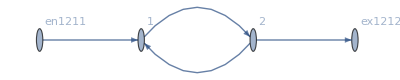

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1213→1,j1214→0,j1215→2,j1216→2,j1217→0,j1218→1,j1219→0,j1220→0,jt1221→0,jt1222→0,jt1223→0,jt1224→0,jt1225→1,jt1226→1,jt1227→0,jt1228→1,jt1229→0,jt1230→1,jt1231→0,jt1232→0,u1233→1,u1234→0,u1235→0,u1236→1,u1237→0,u1238→1,u1239→0,u1240→1|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→19.6805,u1096→19.6805,u1097→17.3402,u1098→17.3402,u1099→17.3402,u1100→15.,u1101→19.6805,u1102→17.3402,u1103→17.3402,u1104→17.3402,u1105→15.,u1106→15.,u1107→15.,u1108→19.6805|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j557-j564-u595+u602==38.3971&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.272367

FRX1: nonlinear: 
j557-j564-u595+u602==52.7699&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0925456

FRX1: nonlinear: 
j557-j564-u595+u602==58.1516&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0334946

FRX1: nonlinear: 
j557-j564-u595+u602==60.1668&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0123877

FRX1: nonlinear: 
j557-j564-u595+u602==60.9215&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00461755

FRX1: nonlinear: 
j557-j564-u595+u602==61.2041&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00172622

FRX1: nonlinear: 
j557-j564-u595+u602==61.3099&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000646026

FRX1: nonlinear: 
j557-j564-u595+u602==61.3496&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000241869

FRX1: nonlinear: 
j557-j564-u595+u602==61.3644&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000905682

FRX1: nonlinear: 
j557-j564-u595+u602==61.37&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000339154

<|j557→63.0137,j558→16.9863,j559→15.3425,j560→47.6712,j561→32.3288,j562→80,j563→80,j564→0.,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0.,jt572→0,jt573→0,jt574→0,jt575→63.0137,jt576→16.9863,jt577→15.3425,jt578→47.6712,jt579→0.,jt580→0.,jt581→0,jt582→0,jt583→0,jt584→16.9863,jt585→0,jt586→15.3425,jt587→0,jt588→0,jt589→0,jt590→47.6712,jt591→0,jt592→32.3288,jt593→0,jt594→0,u595→64.315,u596→64.315,u597→62.6712,u598→62.6712,u599→47.3288,u600→15,u601→64.315,u602→62.6712,u603→47.3288,u604→47.3288,u605→15.,u606→15.,u607→15,u608→64.315|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→23.1887,u1096→23.1887,u1097→19.0944,u1098→19.0944,u1099→19.0944,u1100→15.,u1101→23.1887,u1102→19.0944,u1103→19.0944,u1104→19.0944,u1105→15.,u1106→15.,u1107→15.,u1108→23.1887|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.35438×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.35438×10^-16

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→65.0434,u1096→65.0434,u1097→40.0217,u1098→40.0217,u1099→40.0217,u1100→15.,u1101→65.0434,u1102→40.0217,u1103→40.0217,u1104→40.0217,u1105→15.,u1106→15.,u1107→15.,u1108→65.0434|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j557-j564-u595+u602==0&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[8.52651×10^-14,ComplexInfinity]

<|j557→40,j558→40,j559→0,j560→40,j561→40,j562→80,j563→80,j564→0,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0,jt572→0,jt573→0,jt574→0,jt575→40,jt576→40,jt577→0,jt578→40,jt579→0,jt580→0,jt581→0,jt582→0,jt583→0,jt584→40,jt585→0,jt586→0,jt587→0,jt588→0,jt589→0,jt590→40,jt591→0,jt592→40,jt593→0,jt594→0,u595→95,u596→95,u597→55,u598→55,u599→55,u600→15,u601→95,u602→55,u603→55,u604→55,u605→15,u606→15,u607→15,u608→95|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j557-j564-u595+u602==-178.622&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.52706

FRX1: nonlinear: 
j557-j564-u595+u602==94.1437&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.19236

FRX1: nonlinear: 
j557-j564-u595+u602==-489.411&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.36457

FRX1: nonlinear: 
j557-j564-u595+u602==1342.45&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.12903

FRX1: nonlinear: 
j557-j564-u595+u602==-10403.8&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.05112

FRX1: nonlinear: 
j557-j564-u595+u602==203499.&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.01121

FRX1: nonlinear: 
j557-j564-u595+u602==-1.81556×10^7&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00118

FRX1: nonlinear: 
j557-j564-u595+u602==1.53451×10^10&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00004

FRX1: nonlinear: 
j557-j564-u595+u602==-3.77223×10^14&&j558-j565-u596+u603==6.67572×10^-6&&j559-j566-u597+u604==-3.8147×10^-6&&j560-j567-u598+u605==-2.14577×10^-6&&j561-j568-u599+u606==2.14577×10^-6

FRX1: The last system in the iteration was inconsistent.
Returning the last feasible solution.

FRX1: nonlinear: 
j557-j564-u595+u602==-3.77223×10^14&&j558-j565-u596+u603==6.67572×10^-6&&j559-j566-u597+u604==-3.8147×10^-6&&j560-j567-u598+u605==-2.14577×10^-6&&j561-j568-u599+u606==2.14577×10^-6

FRX1: The last system in the iteration was inconsistent.
Returning the last feasible solution.

```mathematica
<|j557->5.754412314431864*^9,j558->0.,j559->3.8362748496212425*^9,j560->1.9181374648106213*^9,ej561->0.,j562->80,j563->80,j564->0.,j565->5.754412234431864*^9,j566->0,j567->0,j568->1.9181373848106213*^9,j569->0,j570->0,jt571->0.,jt572->0,jt573->5.754412234431864*^9,jt574->0,jt575->80.,jt576->0.,jt577->3.8362748496212425*^9,jt578->1.9181374648106213*^9,jt579->0.,jt580->0.,jt581->0,jt582->0,jt583->0.,jt584->0.,jt585->3.8362748496212425*^9,jt586->0.,jt587->1.9181373848106213*^9,jt588->0.,jt589->1.9181373848106213*^9,jt590->80.,jt591->0,jt592->0.,jt593->0,jt594->0,u595->-7.672549604242487*^9,u596->-7.672549604242487*^9,u597->1.9181374798106213*^9,u598->1.9181374798106213*^9,u599->-1.9181373698106213*^9,u600->15,u601->-7.672549604242487*^9,u602->1.9181374798106213*^9,u603->-1.9181373698106232*^9,u604->-1.9181373698106232*^9,u605->15.,u606->15.,u607->15,u608->-7.672549604242487*^9|>
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→7208.19,u1096→7208.19,u1097→3611.59,u1098→3611.59,u1099→3611.59,u1100→15.,u1101→7208.19,u1102→3611.59,u1103→3611.59,u1104→3611.59,u1105→15.,u1106→15.,u1107→15.,u1108→7208.19|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→2.99468×10^14,u1096→2.99468×10^14,u1097→1.49734×10^14,u1098→1.49734×10^14,u1099→1.49734×10^14,u1100→15.,u1101→2.99468×10^14,u1102→1.49734×10^14,u1103→1.49734×10^14,u1104→1.49734×10^14,u1105→15.,u1106→15.,u1107→15.,u1108→2.99468×10^14|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.707107

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.707107

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→95.,u1096→95.,u1097→55.,u1098→55.,u1099→55.,u1100→15.,u1101→95.,u1102→55.,u1103→55.,u1104→55.,u1105→15.,u1106→15.,u1107→15.,u1108→95.|>